Write out the numerator and denominator in Lekkala2013 θ_I separately.

```mathematica
numerator = Sinh[θ1] Sinh[θ2] - λ Cosh[θ1] Cosh[θ2] + 2 λ - λ^2 Sinh[θ1]/Sinh[θ2]
```

2 λ-λ Cosh[θ1] Cosh[θ2]-λ^2 Csch[θ2] Sinh[θ1]+Sinh[θ1] Sinh[θ2]

```mathematica
denominator = Cosh[θ1] Sinh[θ2] - λ Sinh[θ1] Cosh[θ2]
```

-λ Cosh[θ2] Sinh[θ1]+Cosh[θ1] Sinh[θ2]

At large value of the arguments θ1 and θ2, both numerator and denominator diverge.  However, the ratio seems to remain finite or goes to zero.  Try to rewrite the ratio in a way that avoids the problem.  Divide the numerator by Cosh[θ] to see if that tames the θ1 divergence.

```mathematica
Numerator[ans]/Cosh[θ1] // Simplify
```

-λ Coth[θ2]+2 λ Csch[θ2] Sech[θ1]+Tanh[θ1]-λ^2 Csch[θ2]^2 Tanh[θ1]

After the division, check that the remaining functions of θ1 do not blow up .

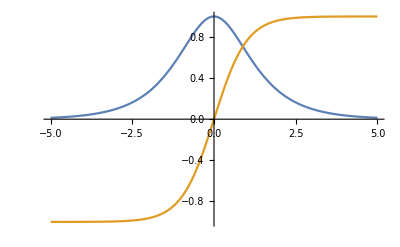

```mathematica
Plot[{Sech[θ1], Tanh[θ1]},{θ1,-5,5}]
```

After the division, the functions of θ2 still blow up .

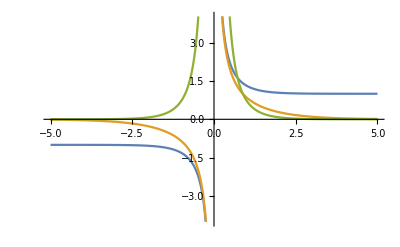

```mathematica
Plot[{Coth[θ2], Csch[θ2],Csch[θ2]^2},{θ2,-5,5}]
```

Divide the denominator by Cosh[θ] to see if that tames the θ1 divergence.

```mathematica
Denominator[ans]/Cosh[θ1] // Simplify
```

1-λ Coth[θ2] Tanh[θ1]

It does ...

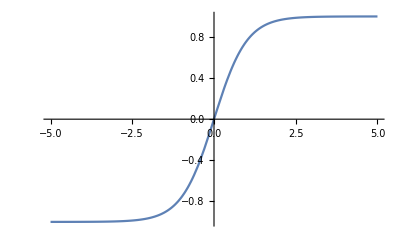

```mathematica
Plot[{Tanh[θ1]},{θ1,-5,5}]
```

... but the θ2 functions in the denominator still diverge.

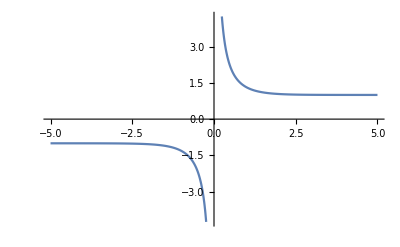

```mathematica
Plot[Coth[θ2],{θ2,-5,5}]
```

Try dividing the denominator by Cosh[θ1]Coth[θ2].

```mathematica
Denominator[ans]/(Cosh[θ1]Coth[θ2]) // Simplify
```

-λ Tanh[θ1]+Tanh[θ2]

Now, by inspection, both the θ1 and θ2 functions in the denominator are well-behaved.  What about the numerator?

```mathematica
Numerator[ans]/(Cosh[θ1]Coth[θ2]) // Simplify
```

-λ+2 λ Sech[θ1] Sech[θ2]-λ^2 Csch[θ2] Sech[θ2] Tanh[θ1]+Tanh[θ1] Tanh[θ2]

All three θ2 functions in the numerator are ok at large θ2.  But one of them diverges at small θ2, which is a problem.

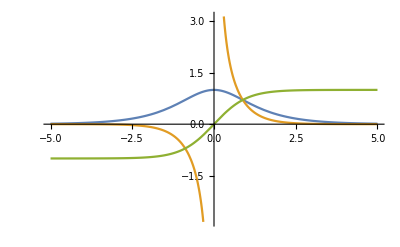

```mathematica
Plot[{Sech[θ2],Csch[θ2] Sech[θ2],Tanh[θ2]},{θ2,-5,5}]
```

This function is the culprit.

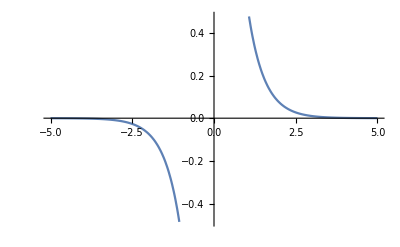

```mathematica
Plot[Csch[θ2] Sech[θ2],{θ2,-5,5}]
```

The argument θ2 = η h_s in the paper, and η does not go to zero.  So, in practice, I think the function Csch[θ2] Sech[θ2] should be ok.

In summary, write the big fraction θ_I as follows

```mathematica
(Tanh[θ1] Tanh[θ2]-λ+2 λ Sech[θ1] Sech[θ2]-λ^2 Tanh[θ1] Csch[θ2] Sech[θ2])/(Tanh[θ2]-λ Tanh[θ1]) ;
```

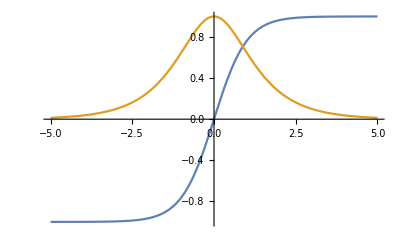

```mathematica
Plot[{Tanh[θ2],Sech[θ2]},{θ2,-5,5}]
```

Python does not have Sech and Csch function.  However, note that

```mathematica
1/Sech[θ1]
```

Cosh[θ1]

```mathematica
1/Csch[θ2]
```

Sinh[θ2]

So we can implement the big fraction θ_I as

```mathematica
θI=(Tanh[θ1] Tanh[θ2]-λ+2 λ /(Cosh[θ1] Cosh[θ2])-λ^2 Tanh[θ1] /(Cosh[θ2] Sinh[θ2]))/(Tanh[θ2]-λ Tanh[θ1]) ;
```

Check that this expression agrees with what we started with.

```mathematica
θI - numerator/denominator // FullSimplify
```

0